```mathematica
Remove["Global`*"]
(*<<PhysicalConstants *)
(*<<Units`*)
(*<<VectorAnalysis`*)
<<FourierSeries`
(*<<LinearRegression`*)
```

```mathematica
(*Range for electrons in Boron*)
(*mid energy range*)
(* mid Range aprox *)

(*eV to μm*)
mideEtR[x_]:=(0.000023405020213207803 x^2)/((1-ⅇ^(-0.01439502363193133 x)) (39.14730830570143/x^2-1.3464447383744376/x+0.015216963656960174 Log[0.12458670986380664 x]))*10^-4; 


(*mideEtR[x_]:=If[69.46845142940786≤x≤20000,(0.000023405020213207803 x^2)/((1-ⅇ^(-0.01439502363193133 x)) (39.14730830570143/x^2-1.3464447383744376/x+0.015216963656960174 Log[0.12458670986380664 x])),0]*10^-4;(*eV to μm*)*)
mideRtE=InverseFunction[10^-4(0.000023405020213207803 #^2)/((1-ⅇ^(-0.01439502363193133 #)) (39.14730830570143/#^2-1.3464447383744376/#+0.015216963656960174 Log[0.12458670986380664 #]))&];(*μm to eV*)

(*low energy range*)
loweEtR[x_]:=(0.04764841875688123 x)/((1-ⅇ^(-0.01439502363193133 x))^2)10^-4; (*eV to μm*)
loweRtE=InverseFunction[loweEtR[#]&]; (*μm to eV*)
R155t10=mideEtR[155];(*μm*)

(*Proton in B11*)
EtPR[x_]:=-4038.621695160617+30.217944902944236/(0.007481857100785539+3.2469601381813174*^-7 ⅇ^(-37.49736075902206 x))+3.307130653753605 x+1515.3152978046726 x^1.9990033267320544-1506.2506067955821 x^2+0.09463470541261623 x^3-0.13448967381673807 x^4+0.047932270219233936 x^5-0.005179352017528617 x^6;(*MeV to µm*)
PRtE= InverseFunction[EtPR[#]&];(*µm to MeV*)

(*Calculate number of particles in the outer shell*)
(*1/{Stopping Power (MeV/µm)}*)
f[x_]:=(4.419276392445275+ⅇ^(-7.3803552653244 (-0.10066107776724603+x))-0.5673657094346726/(1+0.7297860911389368 (-1.1106115256038274+x)^2)+0.5758738282552386/(1+1.030347643016361 (-0.9802921157540312+x)^3)+9.861753173526887 x-0.06433184715293583( x)^2+3.8810193819415244 Log[4.15270754026916 Abs[0.04038187709701176+x]]);
(* 1 cm^2=10^8 μm^2 *)
g[x_]:=10^-20 10^8(9063.081035422943+507.09261348539127/(-0.005818452809878006+0.005423337528382377 ⅇ^(12.826958275846918 x))+1.4880890162138838/(1+61.00372893820754 (-1.5307699305543252+x)^2)-4140.039076082341/x^1.1765976080718534-9274.807826460798 x+5180.027364054856 x^2-1664.2930923111003 x^3+288.4797660880828 x^4-20.91742170821425 x^5+26323.278216356248/(1+9.108208750983506 (0.39062485555934184+x)^4)); (* Cross Section μm^2 *)
```

```mathematica
R155t10
```

0.001658

```mathematica
rBstart=0.0009;(*start boron radius*)
rBFinish=0.0022;(*Finish boron radius*)
rBBins=25; (*number of bins for boron particle radius*)
rBstpsz=(rBFinish-rBstart)/(rBBins-1);
```

```mathematica
eEnProduct=Range[rBBins];
For[ri=1,ri <=rBBins,ri++, 
If[Mod[ri,10]==0,Print[ri]];
rB=rBstart+(ri-1)rBstpsz;(*Boron particle radius in μm*)
(*Calc number of auger electrons in each shell*)
AVGThickCircle=1.5706375999552906;
AVGThick=rB*AVGThickCircle;(*μm*)
EntEnergy=3;(*MeV*)
ExtEnergy=PRtE[EtPR[EntEnergy]-AVGThick];
rBins=20;  (* number of radiuses for different "shells" in boron particle *)
rStepsize=(AVGThick/2(*-AVGThickCircle(rB-R155t10)/2*))/(rBins-1);(*rStepsize=If[(rB-R155t10)>0,(AVGThick/2-AVGThickCircle(rB-R155t10)/2)/(rBins-1),(AVGThick/2)/(rBins-1)];*)
(*step size only has to go through half the particle for differnt radiuses*)
rin=Array[2*(AVGThick/2-(#-1)rStepsize)/1&,rBins];
(* Array of shell thicknesses inside B particle *)
(* Range using energies from max integration *)
(* Need to convert from energy to range and then to energy since stepping through distances and not energy *)
rStart=EtPR[EntEnergy];
rFinish=EtPR[ExtEnergy];
(* innertIntN = array of integrations for shells in B particle, rminEA and rmaxEA are arrays for entering and exiting proton energy used for integration *)
innerIntN=rminEA=rmaxEA=Range[rBins];
For[j=1,j≤rBins,j++,
rmaxE=If[EtPR[0]≤rStart-(j-1)*rStepsize,PRtE[rStart-(j-1)*rStepsize],0];
rminE=If[EtPR[0]≤rFinish+(j-1)*rStepsize,PRtE[rFinish+(j-1)*rStepsize],0];

(*May get a "0" on end of rminEA or rmaxEA but it's "ok" since the integral at center of B11 particle should be zero anyway*)
rmaxE=If[rmaxE<0||rminE>rmaxE||Im[rmaxE]!=0,0,rmaxE];
rminE=If[rminE<0||rminE>rmaxE||Im[rminE]!=0,0,rminE];
innerIntN[[j]]=If[rminE==rmaxE,0, (6.022141×10^23)/10.81*2.3502/10^12*NIntegrate[f[x]*g[x],{x,rminE,rmaxE}]];
rminEA[[j]]=rminE;
rmaxEA[[j]]=rmaxE;
	];

(*Now Find the number of electrons produced in each layer by taking outer - inner*)
CntsSect=Range[Length[innerIntN]-1];
For[k=1,k≤ Length[innerIntN]-1,k++,
CntsSect[[k]]= innerIntN[[k]]-innerIntN[[k+1]];
	]; (* CntsSect is the number of counts in each section- "shell" *)
(*add zero to end since at center zero alpha expected to be produced*)
CntsSect=Append[CntsSect,0];

(* Find average distance traveled by Auger electrons *)
AvgDist=FracProduct=SineDep=Range[rBins];  (*SineDep is the sine dependence since we are only looking at the cross section of a boron particle.*)
For[l=1,l≤rBins,l++,
(*rB;*)(* radius of boron particle *)
(*R155t10;*) (* radius of electron product *)
h=0; (* x-center position of boron particle *)
hk=0;(* y-center position of boron particle *)
x1=rin[[l]]/AVGThickCircle; (* x-center electron r *)
y1=0; (* y-center electron r *)

(* Determine how to calculate the average distance traveled by the auger electrons by first find the the angles of penetration*)

Which[(*if there is no intersection points, but the electron product circe surrounds the boron particle*)Circle[{h,hk},rB]===Circle[{x1,y1},R155t10] (*if each circle is equal there will be no "intersection points"*) ∨ (Length[Quiet[NSolve[{x,y}∈Circle[{h,hk},rB]&&{x,y}∈Circle[{x1,y1},R155t10]]]]==0 ∧ R155t10>rB)(*No intersection points and the radius of the electron product cirlce is larger than the boron cirlce.  Use Quiet to silence NSolve when it can't find any intersection points*),Angles={-π,π}(*Electrons will penetrate across the whole cirlce*),(Length[Quiet[NSolve[{x,y}∈Circle[{h,hk},rB]&&{x,y}∈Circle[{x1,y1},R155t10]]]]==0 ∧ R155t10≤rB) (*If the electron product cirlce is smaller than the boron cirlce and still no intersections then the electrons will not penetrate*),Angles={},Length[NSolve[{x,y}∈Circle[{h,hk},rB]&&{x,y}∈Circle[{x1,y1},R155t10]]]≥1 (*NSolve finds intercepts*),
intersectpts=DeleteDuplicates[{x,y}/.NSolve[{x,y}∈Circle[{h,hk},rB]&&{x,y}∈Circle[{x1,y1},R155t10],{x,y}]];  (*Delete any duplicates that happens when there is one point of penetration*)
Angles=VectorAngle[#,{1,0}]*If[#[[2]]<0,-1,1]&/@intersectpts];(*Find the angles and multiply by 1 or -1 depending on is the angle is positive or negative*)
(*Angles in radians*)

(* based on the angles calculate the average distance *)
(* The FracProduct is the fraction of electrons that escape the boron particle *)
Which[Length[Angles]==0,
	AvgDist[[l]]={} (* No angles: there are no point of penetration so the average distance will be none: {} *); FracProduct[[l]]=0 (* No penetration: The fraction of escaping electrons will be 0 *);
SineDep[[l]]=0(*None*),
	Length[Angles]==1 (* just one point of escape *) ,AvgDist[[l]]=√((intersectpts[[1,1]]-x1)^2+(intersectpts[[1,2]]-y1)^2) (*distance formula*); FracProduct[[l]]=(π/180)/(2π)(* escapes at one degree *)(*1 degree is π/180 radians*);
SineDep[[l]]=Sin[0] (* θ=0 if only one angle *),
	Length[Angles]>1 (* more than one angle of escape *),
	θ1=Angles[[1]];
	θ2=Angles[[2]];
SineDep[[l]]=NIntegrate[Sin[x],{x,0,Abs[θ1]}];
AvgDist[[l]]=NIntegrate[√(((h+rB Cos[t])-x1)^2+((hk+rB Sin[t])-y1)^2)rB ,{t,θ1,θ2}]/NIntegrate[rB,{t,θ1,θ2}];
FracProduct[[l]]=(Abs[θ2]+Abs[θ1])/(2π) (* the simulation uses a symmetry both angles are equal and opposite *);];
];
(*Find the position of numeric values in the AvgDist*)
PosArray=Flatten[Position[AvgDist,#]&/@Select[AvgDist,NumericQ]];  (* Select on the numeric values from average distance using NumericQ
Find their position
Flatten the array *)

(* Add up the AvgDist*CntsSect*FracProduct based on the Position of numceric values.  This is the electron energy product *)
eEnProduct[[ri]]=Total[mideRtE[AvgDist[[#]]]*CntsSect[[#]]*FracProduct[[#]]*SineDep[[#]]&/@PosArray];
]
```

10

20

```mathematica
radii=Array[(rBstart+(#-1)rBstpsz)/1&,rBBins];
```

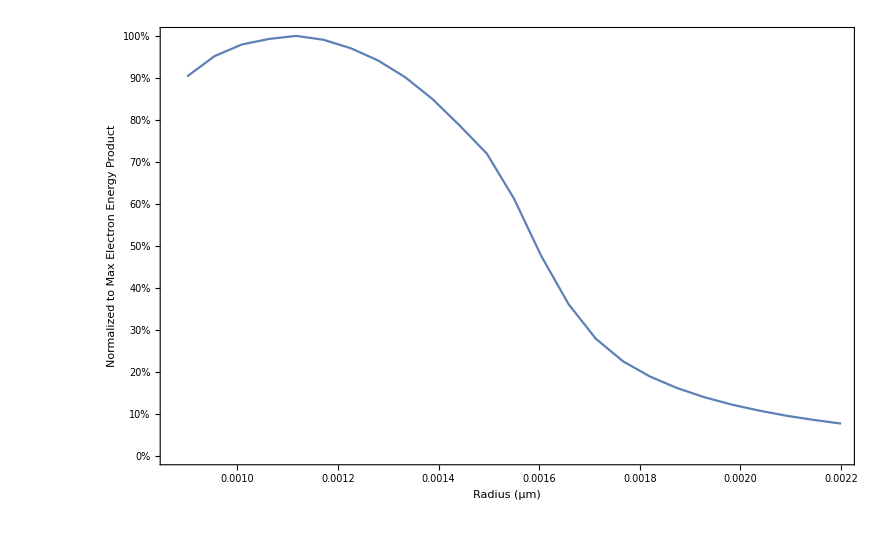

```mathematica
data=Transpose@{radii,eEnProduct/Max[eEnProduct]*100};
ListLinePlot[data,Frame-> True, FrameLabel-> {"Radius (µm)","Normalized to Max Electron Energy Product"},PlotRange-> All,BaseStyle->{FontSize-> 28},FrameTicks->{{{{0.0,"0%"},{10,"10%"},{20,"20%"},{30,"30%"},{40,"40%"},{50,"50%"},{60,"60%"},{70,"70%"},{80,"80%"},{90,"90%"},{100,"100%"}},None},{Automatic,None}}]
```

```mathematica
radii[[Position[eEnProduct,Max[eEnProduct]][[1,1]]]]
```

0.00111667

```mathematica
radii
```

{0.0009,0.000954167,0.00100833,0.0010625,0.00111667,0.00117083,0.001225,0.00127917,0.00133333,0.0013875,0.00144167,0.00149583,0.00155,0.00160417,0.00165833,0.0017125,0.00176667,0.00182083,0.001875,0.00192917,0.00198333,0.0020375,0.00209167,0.00214583,0.0022}

```mathematica
PercentEnProduct=Flatten[eEnProduct/Max[eEnProduct]]*100
```

{87.1444,91.8032,95.3258,97.8418,99.4003,100.,99.5757,97.9856,94.957,89.8944,80.0171,69.7066,63.5816,58.8928,55.0623,51.823,49.0219,46.561,44.373,42.4088}

```mathematica
radii=Array[(rBstart+(#-1)rBstpsz)/1&,rBBins]
```

{0.001,0.00106579,0.00113158,0.00119737,0.00126316,0.00132895,0.00139474,0.00146053,0.00152632,0.00159211,0.00165789,0.00172368,0.00178947,0.00185526,0.00192105,0.00198684,0.00205263,0.00211842,0.00218421,0.00225}

```mathematica
PercentEnProduct={87.1443591155087,91.8031801471894,95.3257638538094,97.84178416253935,99.40029760984778,100.,99.57565697458661,97.98560696229987,94.95703693408062,89.89437499911119,80.01713909236383,69.70662098561206,63.58158595717265,58.89280212193354,55.062313319105904,51.82295784198375,49.021858588893025,46.561020278406964,44.372951250432344,42.40878947137687}
radii={0.001,0.0010657894736842105,0.001131578947368421,0.0011973684210526314,0.0012631578947368421,0.0013289473684210526,0.001394736842105263,0.0014605263157894735,0.0015263157894736842,0.0015921052631578947,0.0016578947368421052,0.0017236842105263156,0.001789473684210526,0.0018552631578947366,0.001921052631578947,0.0019868421052631575,0.0020526315789473684,0.0021184210526315785,0.0021842105263157894,0.00225}
```

{87.1444,91.8032,95.3258,97.8418,99.4003,100.,99.5757,97.9856,94.957,89.8944,80.0171,69.7066,63.5816,58.8928,55.0623,51.823,49.0219,46.561,44.373,42.4088}

{0.001,0.00106579,0.00113158,0.00119737,0.00126316,0.00132895,0.00139474,0.00146053,0.00152632,0.00159211,0.00165789,0.00172368,0.00178947,0.00185526,0.00192105,0.00198684,0.00205263,0.00211842,0.00218421,0.00225}

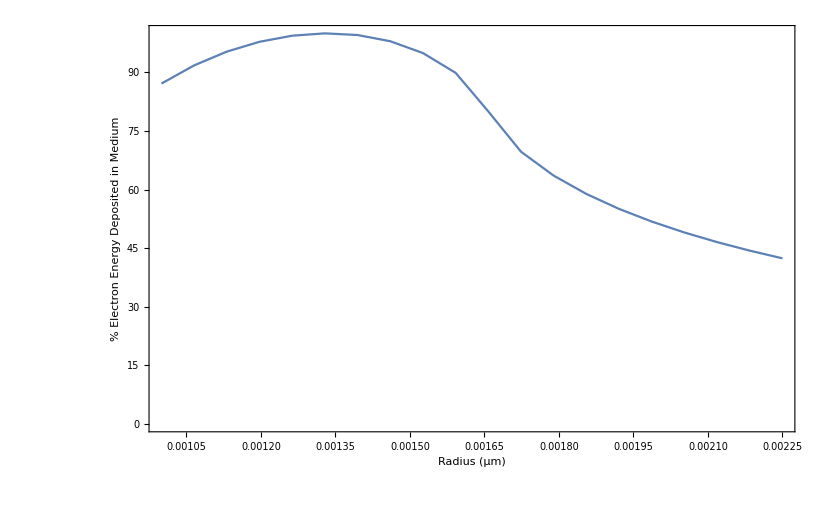

```mathematica
ListLinePlot[{Transpose[{radii,PercentEnProduct}]},PlotRange-> All,Frame->True,BaseStyle->{FontSize-> 28},FrameLabel-> {"Radius (µm)","% Electron Energy Deposited in Medium"}]
```

```mathematica
R155t10
```

0.001658

```mathematica
rin/AVGThickCircle
```

{2.5,1.25,0.}

```mathematica
rin
```

{3.92659,1.9633,0.}

```mathematica
rStepsize
```

0.981648

```mathematica
rin[[1]]-rin[[2]]
```

1.9633

```mathematica
rStepsize=(AVGThick/2)/(rBins-1)(*step size only has to go through half the particle for differnt radiuses*)
rin=Array[2*(AVGThick/2-(#-1)rStepsize)/1&,rBins]
```

0.981648

{3.92659,1.9633,0.}

```mathematica
(rin[[1]]-rin[[2]])/2
```

0.981648

```mathematica
rB*AVGThickCircle
```

3.92659

```mathematica
rin/AVGThickCircle
```

{2.5,1.25,0.}

```mathematica
rStepsize=(AVGThick/2-AVGThickCircle(rB-R155t10)/2)/(rBins-1)(*step size only has to go through half the particle for differnt radiuses*)
rin=Array[2*(AVGThick/2-(#-1)rStepsize)/1&,rBins]
```

0.000651031

{3.92659,3.92529,3.92399}

```mathematica
rin/AVGThickCircle
```

{2.5,2.49917,2.49834}

```mathematica
rin[[1]]/AVGThickCircle-rin[[3]]/AVGThickCircle
```

0.001658

```mathematica
R155t10
```

0.001658

```mathematica
(rin[[1]]+rin[[3]])/2
```

3.92529

```mathematica
innerIntN
```

{4.80389×10^41,4.8023×10^41,4.8007×10^41}

```mathematica
R155t10
```

0.001658